```mathematica
Solve[x^3-3*x^2-6*x+8==0]
```

{{x→-2},{x→1},{x→4}}

```mathematica
Solve[x^2*Abs[x-3]==6x-8]
```

{{x→2},{x→4}}

```mathematica
Solve[√(x+3)==(x^2+2x)/3+1]
```

{{x→-2},{x→1}}

```mathematica
Solve[√(x-8)+3==√(7-x)]
```

{}

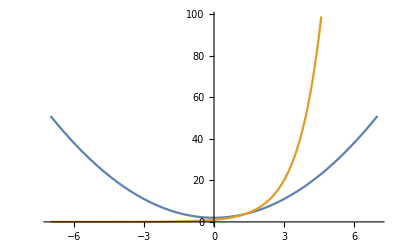

```mathematica
Plot[{x^2+2, ⅇ^x}, {x, -7, 7}]
```

```mathematica
FindRoot[x^2+2==ⅇ^x, {x,1.25}]
```

{1.25→1.31907}

```mathematica
Solve[3+3x-7 x^2-x^3==0]
```

{{x→Root-7.35Root[-3-3 #1+7 #1^2+#1^3&,1]-7.352528664298343},{x→Root-0.486Root[-3-3 #1+7 #1^2+#1^3&,2]-0.4863758458868546},{x→Root0.839Root[-3-3 #1+7 #1^2+#1^3&,3]0.8389045101851978}}

```mathematica
Solve[Sin[x]*Sin[3x]==1/2]
```

{{x→ConditionalExpression[-(5 π)/6+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[-(3 π)/4+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[-π/4+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[-π/6+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[π/6+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[π/4+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[(3 π)/4+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[(5 π)/6+2 π C[1], C[1]∈ℤ]}}

```mathematica
Solve[Sin[x]+Cos[x]+Sin[x]*Cos[x]==1, x]
```

{{x→ConditionalExpression[2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[π/2+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[-π+ArcTan[(-3-ⅈ √7)/(-3+ⅈ √7)]+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[-π+ArcTan[(-3+ⅈ √7)/(-3-ⅈ √7)]+2 π C[1], C[1]∈ℤ]}}

Solve::ivar: 1.25 is not a valid variable.

```mathematica
Solve[{x*y-29==x+y, x^2+y^2==x+y+72}, {x, y}]
```

{{x→6,y→7},{x→7,y→6},{x→-5-√6,y→-5+√6},{x→-5+√6,y→-5-√6}}

Solve::ivar: 1.25 is not a valid variable.

LinearSolve::matrix: Argument {v+2 x+y-z==5,t+2 x+y-z==11,t+v+2 x-z==17,t+v+2 x+y==-1,t+v+y-z==0} at position 1 is not a non-empty rectangular matrix.

```mathematica
LinearSolve[{{2, 1, -1, 1, 0}, {2, 1,-1,0,1},{2,0,-1,1,1},{2,1,0,1,1},{0,1,-1,1,1}},{5,11,17,-1,0}]
```

{4,-9,-9,-3,3}